Henry's Law for Gases Dissolved in Water

```mathematica
AH={-156.51,-159.854,-171.764,-250.812,-153.027,-105.9768,-125.939,-338.217,-181.587,-171.2542};
```

```mathematica
BH={8160.2,8741.68,8296.9,12695.6,7965.2,4259.62,5528.45,13282.1,8632.12,8319.24};
```

```mathematica
CH={21.403,21.6694,23.3376,34.7413,20.5248,14.0094,16.8893,51.9144,24.7981,23.24323};
```

```mathematica
DH={0,-1.10261*^-3,0,0,0,0,0,-0.0425831,0,0};
```

```mathematica
Manipulate[
Module[{newdata,species,col,H,x},
newdata[data_]:=Delete[data,Position[{acetylene,carbondioxide,carbonmonoxide,ethane,ethylene,helium,hydrogen,methane,nitrogen,oxygen},False]];
species=newdata@{"acetylene","carbon dioxide","carbon monoxide","ethane","ethylene","helium","hydrogen","methane", "nitrogen","oxygen" };
col=newdata@{RGBColor[0.5, 0., 0.],RGBColor[1., 0., 0.],RGBColor[1., 0.4974129911626398, 0.],RGBColor[Rational[218, 255], Rational[11, 17], Rational[32, 255]],RGBColor[0., 0.7896136719636774, 0.3371065195394848],RGBColor[0., 0.44148698824292576, 0.7932403760642176],RGBColor[0, 0, 1],RGBColor[0.5, 0, 0.5],Hue[0.9],RGBColor[0.5, 0.5, 0.5]};

H=1/Exp[AH+BH/(t+273)+CH*Log[t+273]+DH*(t+273)];
x=newdata[P/H];
(*
Column[{
(*Plot[x,{t,0,250},PlotStyle->col,FrameLabel->{Style["temperature (°C)",17],Style["mole  fraction  gas  in  water ",17]},PlotRangePadding->{None,Scaled[0.02]},PlotRangeClipping->False,PlotRange->All,Axes->False,Frame->True,LabelStyle->{14,Black},ImageSize->{600,370},AspectRatio->Full,ImagePadding->{{70,60},{75,20}},PlotRange->If[Length@x>0,{0,Max@Table[newdata@(5/H),{t,0,250}]},All]],*)
Plot[x,{t,0,250},PlotStyle->col,FrameLabel->{Style["temperature (°C)",17],Style["mole  fraction  gas  in  water ",17]},PlotRangePadding->{None,Scaled[0.02]},PlotRangeClipping->False,Epilog->Table[Mouseover[{Transparent,Line[Table[{t,x[[i]]},{t,0,250}]]},Text[Style[species[[i]],17,col[[i]],Background->White],Dynamic@MousePosition["Graphics"],{0,-1.5}]],{i,1,Length@x}],
Axes->False,Frame->True,LabelStyle->{14,Black},ImageSize->{600,370},AspectRatio->Full,ImagePadding->{{70,60},{75,20}},PlotRange->If[Length@x>0,{0,Max@Table[newdata@(5/H),{t,0,250}]},All]],*)
(**)
Show[Switch[npr,
True,
BarChart[x/.t->T,ChartStyle->col,ChartLabels->Placed[Rotate[Style[#,17],30 °]&/@species,{{0.5,0},{0.9,1}}],FrameTicks->{{True,True},{None,None}},FrameLabel->{None,Style["mole  fraction  gas  in  water ",17]},PlotRangePadding->{None,{None,Scaled[0.02]}}],
False,
Plot[x,{t,0,250},PlotStyle->col,FrameLabel->{Style["temperature (°C)",17],Style["mole  fraction  gas  in  water ",17]},PlotRangePadding->{None,Scaled[0.02]},PlotRangeClipping->False,(*PlotRange->All,*)Epilog->Table[Mouseover[{Transparent,Line[Table[{t,x[[i]]},{t,0,250}]]},Text[Style[species[[i]],17,col[[i]],Background->White],Dynamic@MousePosition["Graphics"],{0,-1.5}]],{i,1,Length@x}]]
],
Axes->False,Frame->True,LabelStyle->{14,Black},ImageSize->{600,370},AspectRatio->Full,ImagePadding->{{70,60},{75,20}},PlotRange->If[Length@x>0,{0,Max@Table[newdata@(5/H),{t,0,250}]},All]]
],
Grid[{
{Style["select species to plot: ",Bold],
Control[{{acetylene,False,Style["acetylene",RGBColor[0.5, 0., 0.]]},{True,False}}],
Control[{{carbondioxide,False,Style["carbon dioxide",RGBColor[1., 0., 0.]]},{True,False}}],
Control[{{carbonmonoxide,False,Style["carbon monoxide",RGBColor[1., 0.4974129911626398, 0.]]},{True,False}}],
Control[{{ethane,False,Style["ethane",RGBColor[Rational[218, 255], Rational[11, 17], Rational[32, 255]]]},{True,False}}],
Control[{{ethylene,False,Style["ethylene",RGBColor[0., 0.7896136719636774, 0.3371065195394848]]},{True,False}}]},
{Spacer[1],
Control[{{helium,True,Style["helium",RGBColor[0., 0.44148698824292576, 0.7932403760642176]]},{True,False}}],
Control[{{hydrogen,False,Style["hydrogen",RGBColor[0, 0, 1]]},{True,False}}],
Control[{{methane,False,Style["methane",RGBColor[0.5, 0, 0.5]]},{True,False}}],
Control[{{nitrogen,False,Style["nitrogen",Hue[0.9]]},{True,False}}],
Control[{{oxygen,False,Style["oxygen",RGBColor[0.5, 0.5, 0.5]]},{True,False}}]}
},Alignment->Right],
Spacer[1],
Grid[{{
Control[{{npr,False,"set temperature"},{True,False}}],Spacer[5],
Control[{{P,1(*5*),"partial pressure (bars)"},1,5,0.1,Appearance->"Labeled",ImageSize->Tiny}],
PaneSelector[{True->Control[{{T,0,"temperature (°C)"},0,250,1,Appearance->"Labeled",ImageSize->Tiny}]},Dynamic@npr]
}}],
SaveDefinitions->True]
```

```mathematica
(*Grid[{
{Style["select species to plot: ",Bold],
Control[{{acetylene,True,Style["acetylene",RGBColor[0.5, 0., 0.]]},{True,False}}],
Control[{{carbondioxide,True,Style["carbon dioxide",RGBColor[1., 0., 0.]]},{True,False}}],
Control[{{carbonmonoxide,True,Style["carbon monoxide",RGBColor[1., 0.4974129911626398, 0.]]},{True,False}}],
Control[{{ethane,True,Style["ethane",RGBColor[Rational[218, 255], Rational[11, 17], Rational[32, 255]]]},{True,False}}],
Control[{{ethylene,True,Style["ethylene",RGBColor[0., 0.7896136719636774, 0.3371065195394848]]},{True,False}}]},
{Spacer[1],
Control[{{helium,True,Style["helium",RGBColor[0., 0.44148698824292576, 0.7932403760642176]]},{True,False}}],
Control[{{hydrogen,True,Style["hydrogen",RGBColor[0, 0, 1]]},{True,False}}],
Control[{{methane,True,Style["methane",RGBColor[0.5, 0, 0.5]]},{True,False}}],
Control[{{nitrogen,True,Style["nitrogen",Hue[0.9]]},{True,False}}],
Control[{{oxygen,True,Style["oxygen",RGBColor[0.5, 0.5, 0.5]]},{True,False}}]}
},Alignment->Right],*)
```

```mathematica
0.2125
```

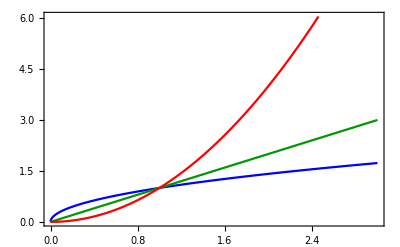
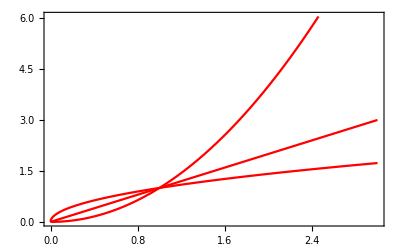
-Graphics--Graphics--Graphics-

```mathematica
Module[{f1,f2,opt,col},
f1={x^(1/2),x,x^2};
f2[x_]:={x^(1/2),x,x^2};

opt=Sequence[Frame->True,ImageSize->400];
col={RGBColor[0, 0, 1],RGBColor[0, 0.6, 0],RGBColor[1, 0, 0]};

Row[{
Plot[f1,{x,0,3},PlotStyle->col,Evaluate@opt],
Plot[f2[x],{x,0,3},PlotStyle->col,Evaluate@opt],
Plot[Through@f1@x,{x,0,3},PlotStyle->col,Evaluate@opt]
}]
]
```

```mathematica
Module[{f,col},
f={x+5,x^1.5+10,x^2+15};
col={RGBColor[0, 0, 1],RGBColor[0, 0.6, 0],RGBColor[1, 0, 0]};

Plot[f,{x,0,5},PlotStyle->col,Frame->True,ImageSize->500];

Min@Table[{x,f},{x,0,5}][[#,All]]&/@Range@6;

{#-1,Min@Table[f,{x,0,5}][[#,All]]}&/@Range@6
]
```

{{0,5},{1,6},{2,7},{3,8},{4,9},{5,10}}

This Demonstration runs calculations of the mole fraction for 10 different gases dissolved in water. For the gases whose boxes are checked, a bar graph for mole fraction versus temperature is shown. When the "set temperature" box is checked, you can use the temperature slider to compare the mole fractions of each gas dissolved in water, as shown on the bar graph. When "set temperature" is not selected, the mole fractions are plotted versus temperature; hover the cursor over a curve to see which gas it corresponds to. The partial pressure can also be varied by a slider.

Henry's constant H varies with temperature, as given by:

H=1/exp(A+B/T+C ln T+D T),

where H is in bars; A, B, C, and D are constants specific to each species; and T is temperature (K).

Henry's law is used to calculate the mole fraction x of a species dissolved in water:

x H=P,

where P is the partial pressure (bar).

Reference

[1] B. E. Poling, G. H. Thomson, D. G. Friend, R. L. Rowley, and W. V. Wilding, "Physical and Chemical Data," Perry's Chemical Engineers' Handbook (D. W. Green and R. H. Perry, eds.), 8th ed., New York: McGraw-Hill, 2008.

Resize Images

Rotate and Zoom in 3D

Drag Locators

Create and Delete Locators

Slider Zoom

Gamepad Controls

Automatic Animation

Bookmark Animation

Henry's law

solubility

chemical engineering

Temperature Dependence of Henry's Law Constant

Contributed by: Rachael L. Baumann

Additional contributions by: John L. Falconer

(University of Colorado Boulder, Department of Chemical and Biological Engineering)